```mathematica
myIntegrate[f_,a_,b_,eps_]:=(
n=2;
h=(b-a)/n;
Do[Subscript[x, i]=i*h,{i,0,n}];
IApprox1= (b-a)/n∑_(j=1)^n f[(Subscript[x, j-1]+Subscript[x, j])/2]//N;
Do[(
n++;
h=(b-a)/n;
Do[Subscript[x, i]=i*h,{i,0,n}];
IApprox2= (b-a)/n∑_(j=1)^n f[(Subscript[x, j-1]+Subscript[x, j])/2]//N;
If[Abs[IApprox1-IApprox2]<eps,Break[]];
IApprox1=IApprox2;
),1000];
Print["Iterations = ",n];
Print[Show[Plot[f[x],{x,a,b}],DiscretePlot[f[x],{x,a,b,h},ExtentSize->Full]]];
N[IApprox2,10]
)
```

```mathematica
f[x_]=1-E^(-x)
```

1-ⅇ^-x

Iterations = 25

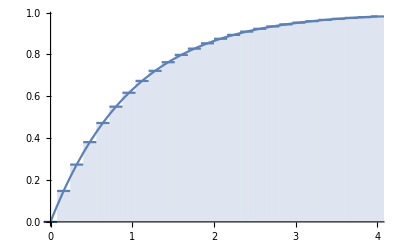

Set::wrsym: Symbol ⅈ is Protected.

3.01936

```mathematica
I = myIntegrate[f,0,4,10^(-4)]
```

```mathematica
Integrate[f[x],{x,0,4}]//N
```

3.01832